#### params

```mathematica
Δ=5*10^-3;0.005;
σ=0.01;
α=0.001;
ϕ=0.001;
γ=10;
κ=50;
ε=0.005;
Υ=Δ+ε;
χ=0.02;
tiltλ=50/300;
λ=N[50/300];


Ν=10;(*Total Amt*)
T=300;(*Total Time*)
```

```mathematica
λ
```

0.1298

```mathematica
(*Market Impact Cost*)
c[q_]:=α*q;
```

```mathematica
(*Target Schedule*)
IS[t_]:=Ν*(1-Sinh[χ*(T-t)]/Sinh[χ*T])
```

#### eqs

```mathematica
ω[t_,q_]:=ⅇ^(-κ*(Υ+c[Ν-q])*(Ν-q))/;t==T
ω[t_,q_]:=Exp[-κ*ϕ*NIntegrate[(Ν-IS[u])^2,{u,t,T}]]/;q==Ν
```

尝试解析解 建议告辞

```mathematica
eqs=(D[ω[t,q],t]-κ*ϕ*(q-IS[t])^2 ω[t,q]+ⅇ^-1 λ ω[t,q+1])*(ω[t,q]-ⅇ^(-κ*Υ)ω[t,q+1])==0
```

(ω[t,q]-0.606531 ω[t,1+q]) (-0.05 (q-10 (1-0.00495753 Sinh[0.02 (300-t)]))^2 ω[t,q]+0.122626 ω[t,1+q]+ω^(1,0)[t,q])==0

数值解尝试
Do it backwards

```mathematica
fdmSolver[t_,nt_,q_]:=
Module[
{time=N@Subdivide[0,t,nt-1],
dt,
mat,
idxTrigger,
trigger
},
dt=First@Differences@time;
mat=ConstantArray[0,{q+1,Length[time]}];
mat[[-1]]=Table[ω[i,q],{i,time}];
trigger=ConstantArray[0,{q+1, Length[time]}];
trigger[[;;,-1]]=ConstantArray[1,q+1];
(*from t+dt to t*)
Do[
mat[[1;;-2,idxT]]=
mat[[1;;-2,idxT+1]]-
κ*ϕ*dt*
Thread[
Times[
Power[Range[0,q-1]-IS[time[[idxT+1]]],2],
mat[[1;;-2,idxT+1]]]]
+ⅇ^-1*λ*dt*mat[[2;;-1,idxT+1]];
(*idxTrigger=Boole[Table[Less[mat[[;;,idxT]][[i]], mat[[;;,idxT]][[i+1]]*ⅇ^(-κ*Υ)],{i,1,q}]];
PrependTo[idxTrigger,0];
trigger[[1;;-1,idxT]]=idxTrigger;*)
(*mat[[1;;-2,idxT]]*ⅇ^(-κ*Υ)≥ mat[[2;;-1,idxT]];*)
mat[[1;;-2,idxT]]=MapThread[Max,{ⅇ^(-κ*Υ)*mat[[2;;-1,idxT]],mat[[1;;-2,idxT]]}];
,
{idxT,Range[Length[time]-1,1,-1]}];
{mat, trigger}
]
```

```mathematica
{mat, trigger}=fdmSolver[T,3000,10]
```

{{{19.3204,19.1605,19.0007,18.841,18.6815,18.5224,18.3637,18.2056,18.0481,17.8914,17.7356,17.5807,17.4268,17.274,17.1225,16.9722,16.8232,16.6757,16.5297,16.3853,16.2425,16.1015,2956,0.00151728,0.00151026,0.00150321,0.00149612,0.001489,0.00148185,0.00147467,0.00146745,0.0014602,0.00145291,0.00144559,0.00143824,0.000172554,7.41901×10^-6,1.28548×10^-7,7.65091×10^-10,7.12458×10^-13,0.,0.,0.,0.,0},9,{1}},{1}}
 |  |  |  |

```mathematica
MapThread[Max,{ⅇ^(-κ*Υ)*mat[[2;;-1,102]],mat[[1;;-2,102]]}]
```

{8.49839,14.0115,23.101,25.4861,9.83948,0.666341,0.00303203,2.48084×10^-7,5.88854×10^-14,2.68366×10^-24}

```mathematica
Length@%
```

10

```mathematica
r =Thread[mat[[1]]≥ ⅇ^(-κ*Υ)*mat[[2]]];
```

```mathematica
SelectFirst[Range[Length[r]],r[[#]]==False&]
```

102

```mathematica
mat[[1,102]]
```

8.49679

```mathematica
mat[[All,102]]
```

{8.49679,14.0115,23.101,25.4861,9.83948,0.666341,0.00303203,2.48084×10^-7,5.88854×10^-14,2.68366×10^-24,5.86007×10^-37}

```mathematica
mat[[All,102]][[1;;-2]]
```

{8.49679,14.0115,23.101,25.4861,9.83948,0.666341,0.00303203,2.48084×10^-7,5.88854×10^-14,2.68366×10^-24}

```mathematica
mat[[All,102]][[2;;-1]]
```

{14.0115,23.101,25.4861,9.83948,0.666341,0.00303203,2.48084×10^-7,5.88854×10^-14,2.68366×10^-24,5.86007×10^-37}

```mathematica
Thread[mat[[1;;-2,102]]≥ ⅇ^(-κ*Υ)*mat[[2;;-1,102]]]
```

{False,True,True,True,True,True,True,True,True,True}

```mathematica
{mat,trigger}=fdmSolver[T,3000,Ν];
```

```mathematica
ListPlot3D@mat
```

-Graphics3D-

```mathematica
mat[[1;;-2,3]]
```

{19.0007,26.0875,17.0487,3.12083,0.0824413,0.00013006,3.87147×10^-9,4.71262×10^-16,2.80962×10^-26,3.45641×10^-41}

```mathematica
MapThread[Max,{ⅇ^(-κ*Υ)*mat[[2;;-1,3]],mat[[1;;-2,3]]}]
```

{19.0007,26.0875,17.0487,3.12083,0.0824413,0.00013006,3.87147×10^-9,4.71262×10^-16,2.80962×10^-26,3.45641×10^-41}

```mathematica
MapThread[Max,{ⅇ^(-κ*Υ)*mat[[2;;-1,1]],mat[[1;;-2,1]]}]
```

{19.3204,26.0492,16.4303,2.85246,0.0699569,0.000099908,2.61419×10^-9,2.70064×10^-16,1.30792×10^-26,1.23419×10^-41}

```mathematica
Dimensions@trigger
```

{11,3000}

```mathematica
ListPlot3D@trigger
```

-Graphics3D-

```mathematica
findTrigger[triggerMat_,time_]:=
time[[Table[
With[{row=triggerMat[[idxQ,All]]},
SelectFirst[
Range[Length@row],
row[[#]]==1&]],{idxQ,Length@triggerMat-1}]]]
```

```mathematica
t=findTrigger[trigger,N@Subdivide[0,300,3000-1]]
```

{300.,3.70123,9.6032,16.2054,24.008,33.2111,44.7149,59.8199,82.2274,125.342}

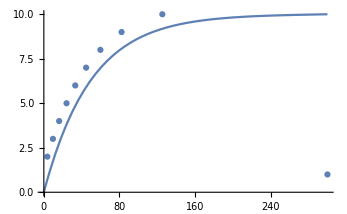

```mathematica
ListPlot[Transpose[{t,Range[Ν]}]]~Show~Plot[IS[i],{i,0,300}]
```

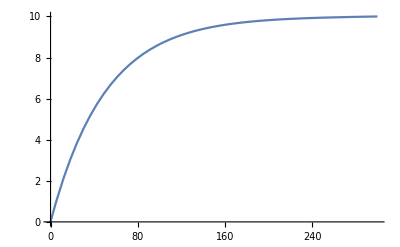

```mathematica
Plot[IS[i],{i,0,300}]
```

```mathematica
{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1}}[[;;-2]]
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1}}

#### Price Dynamics

```mathematica
S0=100
```

100

```mathematica
𝒫=TransformedProcess[S0+σ*(up[t]-down[t]),{up\[Distributed]PoissonProcess[γ],down\[Distributed]PoissonProcess[γ]},t];
```

```mathematica
data = RandomFunction[𝒫,{0,T,1},10]
```

TemporalData[…]

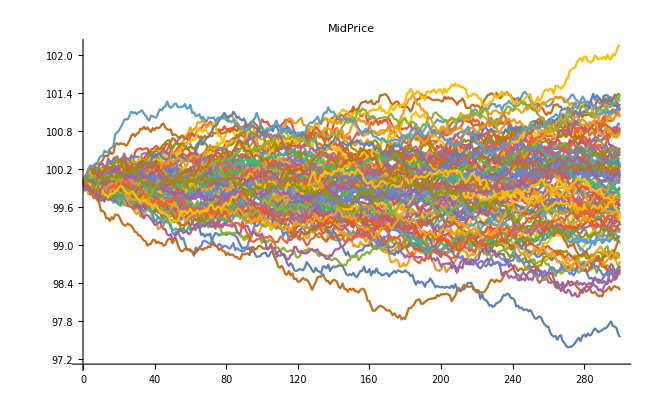

```mathematica
ListLinePlot[ RandomFunction[𝒫,{0,T,1},100],PlotLabel->"MidPrice"]
```